```mathematica
mt =ImageData[-Graphics-//Binarize];
```

```mathematica
Image /@ Transpose/@ SplitBy[mtᵀ,MatchQ[#,{0..}]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
out ={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
outraw = Transpose/@ SplitBy[mtᵀ,MatchQ[#,{0..}]&]
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,1,0,0},{0,0,0,0,1,1,1,1,1,1,1,1,1},{0,0,0,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,0,0,0,0,1,1,1,0},{0,0,1,1,0,0,0,0,0,1,1,0,0},{0,1,1,1,1,1,0,0,1,1,1,0,0},{0,1,1,0,1,1,1,0,1,1,0,0,0},{1,1,0,0,1,1,1,1,1,1,0,0,0},{0,0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,0},{0,0,0,0,0,1,1,1,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,1,1,1,1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}},{{0,0},{0,0},{0,0},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}},{{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{0,0,1,1},{1,1,1,1},{1,1,1,1},{0,1,1,0}}}

```mathematica
ArrayPlot[#, ColorRules->{0->Black, 1->White}, Mesh->True] & /@ outraw
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Flatten[{ {{0,1},{1,0}}, {{2},{3}} },2]
```

{0,1,1,0,2,3}

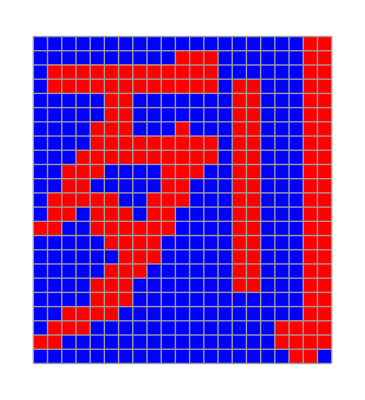

```mathematica
Join[##, 2]&@@Table[outraw[[i]],{i, 1,outraw//Length}]//ArrayPlot[#, ColorRules->{0->Blue, 1->Red}, Mesh->True] &
```

```mathematica
Array[_&,3]
```

{_,_,_}

```mathematica
{1,2, 3} /. {1->x, 2->y, 3->z}
```

{x,y,z}

```mathematica
{{{0,0},{0,0}},{{1,1}},{{0,0}} } // Flatten[#,1]&
```

{{0,0},{0,0},{1,1},{0,0}}

```mathematica
SplitBy[mtᵀ,MatchQ[#,{0..}]&]// Flatten[#,1]& // Transpose // ArrayPlot[#, ColorRules->{0->Black, 1->White}, Mesh->True] &
```

-Graphics-